## signalling model

we are going to make a model of a signalling circuit

to do list:
1. rate equations
2. rate of change equations, differential equations
3. parameters and initial conditions
4. combine this information into one mathematica-interpretable model
5. feed it to a solver
6. solve it and plot the result.

### model definition

```mathematica
rateequations={
v1-> k1f r[t]^2-k1b r2[t],
v2->k2f r2[t] s-k2b sr2[t],
v3->k3f r2[t] s-k3b r2s[t],
v4->k4f sr2[t] s-k4b sr2s[t],
v5->k5f r2s[t] s-k5b sr2s[t],
v6->k6f sr2s[t]-k6b sr2cs[t],
v7->k7f sr2cs[t] T[t]-k7b sr2scT[t]};
odes={
r'[t]==-2 v1,
r2'[t]==v1-v2-v3,
sr2'[t]==v2-v4,
r2s'[t]==v3-v5,
sr2s'[t]==v4+v5-v6,
sr2cs'[t]==v6-v7,
sr2scT'[t]==v7,
T'[t]==-v7};
```

```mathematica
odes/.rateequations//TableForm
```

r'[t]==-2 (k1f r[t]^2-k1b r2[t])
r2'[t]==k1f r[t]^2-k1b r2[t]-k2f s r2[t]-k3f s r2[t]+k3b r2s[t]+k2b sr2[t]
sr2'[t]==k2f s r2[t]-k2b sr2[t]-k4f s sr2[t]+k4b sr2s[t]
r2s'[t]==k3f s r2[t]-k3b r2s[t]-k5f s r2s[t]+k5b sr2s[t]
sr2s'[t]==k5f s r2s[t]+k4f s sr2[t]+k6b sr2cs[t]-k4b sr2s[t]-k5b sr2s[t]-k6f sr2s[t]
sr2cs'[t]==-k6b sr2cs[t]+k6f sr2s[t]+k7b sr2scT[t]-k7f sr2cs[t] T[t]
sr2scT'[t]==-k7b sr2scT[t]+k7f sr2cs[t] T[t]
T'[t]==k7b sr2scT[t]-k7f sr2cs[t] T[t]

```mathematica
parameters={
s->10,
k1f->10,k1b->1,
k2f->10,k2b->1,
k3f->10,k3b->1,
k4f->10,k4b->1,
k5f->10,k5b->1,
k6f->10,k6b->1,
k7f->10,k7b->1};
```

```mathematica
odes/.rateequations/.parameters//TableForm
```

r'[t]==-2 (10 r[t]^2-r2[t])
r2'[t]==10 r[t]^2-201 r2[t]+r2s[t]+sr2[t]
sr2'[t]==100 r2[t]-101 sr2[t]+sr2s[t]
r2s'[t]==100 r2[t]-101 r2s[t]+sr2s[t]
sr2s'[t]==100 r2s[t]+100 sr2[t]+sr2cs[t]-12 sr2s[t]
sr2cs'[t]==-sr2cs[t]+10 sr2s[t]+sr2scT[t]-10 sr2cs[t] T[t]
sr2scT'[t]==-sr2scT[t]+10 sr2cs[t] T[t]
T'[t]==sr2scT[t]-10 sr2cs[t] T[t]

intermediate calculation for the  initial conditions  of the receptor in the absence of the signal

```mathematica
Solve[{
R2==10 R^2,
R+2R2==10},{R,R2}]//N
```

{{R→-0.732549,R2→5.36627},{R→0.682549,R2→4.65873}}

```mathematica
initialconditions={
r[0]==0.6825485849042453,
r2[0]==4.658725707547878,
sr2[0]==0,
r2s[0]==0,
sr2s[0]==0,
sr2cs[0]==0,
sr2scT[0]==0,
T[0]==4};
```

integrate all the  information

```mathematica
model=Join[odes/.rateequations/.parameters,initialconditions];
model//TableForm
```

r'[t]==-2 (10 r[t]^2-r2[t])
r2'[t]==10 r[t]^2-201 r2[t]+r2s[t]+sr2[t]
sr2'[t]==100 r2[t]-101 sr2[t]+sr2s[t]
r2s'[t]==100 r2[t]-101 r2s[t]+sr2s[t]
sr2s'[t]==100 r2s[t]+100 sr2[t]+sr2cs[t]-12 sr2s[t]
sr2cs'[t]==-sr2cs[t]+10 sr2s[t]+sr2scT[t]-10 sr2cs[t] T[t]
sr2scT'[t]==-sr2scT[t]+10 sr2cs[t] T[t]
T'[t]==sr2scT[t]-10 sr2cs[t] T[t]
r[0]==0.682549
r2[0]==4.65873
sr2[0]==0
r2s[0]==0
sr2s[0]==0
sr2cs[0]==0
sr2scT[0]==0
T[0]==4

```mathematica
variables={r,r2,sr2,r2s,sr2s,sr2cs,sr2scT,T};
```

```mathematica
tsol=NDSolve[model,variables,{t,0,1}];
```

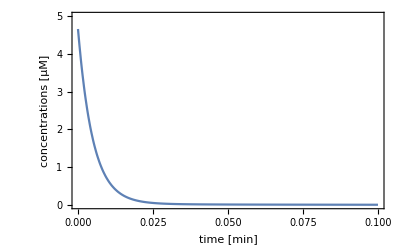

```mathematica
plA=Plot[r2[t]/.tsol,{t,0,0.1},PlotRange->{{0,0.1},{0,5}},Frame->True,FrameLabel->{"time [min]","concentrations [μM]"},BaseStyle->{FontSize->14},PlotPoints->100]
```

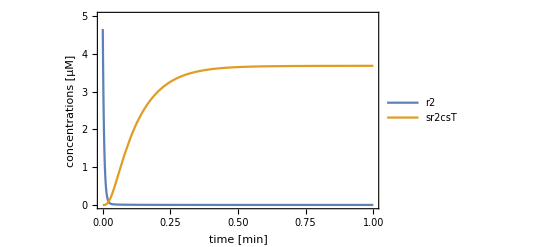

```mathematica
plB=Plot[{r2[t]/.tsol,sr2scT[t]/.tsol},{t,0,1},PlotRange->{{0,1},{0,5}},Frame->True,FrameLabel->{"time [min]","concentrations [μM]"},BaseStyle->{FontSize->14},PlotLegends->{"r2","sr2csT"}]
```

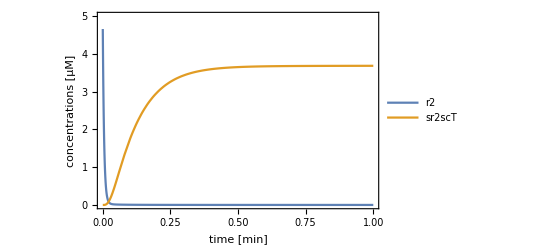

```mathematica
Plot[{r2[t]/.tsol,sr2scT[t]/.tsol},{t,0,1},PlotRange->{{0,1},{0,5}},Frame->True,FrameLabel->{"time [min]","concentrations [μM]"},BaseStyle->{FontSize->14},PlotLegends->Placed[LineLegend[{"r2","sr2scT" },LegendLayout->{"Column",1},LabelStyle->{FontFamily->"Helvetica",FontSize->15},LegendMarkerSize->{20,15}],{0.85,0.2}]]
```